```mathematica
glocal=9.768892463
```

```mathematica
Length[data]
```

5000

```mathematica
FFTData=Fourier[data/glocal,FourierParameters->{-1,1}]
```

{-1.02644×10^-6+3.28567×10^-25 ⅈ,-1.5682×10^-7+2.27716×10^-8 ⅈ,-1.58728×10^-7+3.37545×10^-8 ⅈ,-1.77508×10^-7+2.23834×10^-8 ⅈ,4992,-3.38675×10^-7+6.82071×10^-8 ⅈ,-1.77508×10^-7-2.23834×10^-8 ⅈ,-1.58728×10^-7-3.37545×10^-8 ⅈ,-1.5682×10^-7-2.27716×10^-8 ⅈ}
 |  |  |  |

```mathematica
(FFTData-Fourier[data/9.81,FourierParameters->{-1,1}])/FFTData (*Not too significant a correction*)
```

{0.00419037+4.1061×10^-35 ⅈ,0.00419037+8.2148×10^-17 ⅈ,0.00419037-5.47335×10^-18 ⅈ,0.00419037-1.37518×10^-16 ⅈ,0.00419037+1.64728×10^-17 ⅈ,4991,0.00419037+1.42444×10^-17 ⅈ,0.00419037+2.09795×10^-16 ⅈ,0.00419037-1.55885×10^-16 ⅈ,0.00419037+2.87399×10^-17 ⅈ}
 |  |  |  |

```mathematica
(*ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@FFTData,AspectRatio->1]*)
```

```mathematica
FFTData//ExpToTrig
```

{-0.0000100272+3.20973×10^-24 ⅈ,-1.53196×10^-6+2.22454×10^-7 ⅈ,-1.5506×10^-6+3.29744×10^-7 ⅈ,-1.73406×10^-6+2.18661×10^-7 ⅈ,4992,-3.30848×10^-6+6.66308×10^-7 ⅈ,-1.73406×10^-6-2.18661×10^-7 ⅈ,-1.5506×10^-6-3.29744×10^-7 ⅈ,-1.53196×10^-6-2.22454×10^-7 ⅈ}
 |  |  |  |

```mathematica
Time=Table[(4/5000)*n,{n,1,5000}]//N
```

```mathematica
Time[[1]]
```

0.

```mathematica
Freqs=Table[1/Time[[n]],{n,1,5000}]//N
```

```mathematica
Length[Freqs]
```

5000

```mathematica
Data=Table[{Freqs[[i]],FFTData[[i]]},{i,1,5000}]
```

```mathematica
MatrixPlot[Data]
```

```mathematica
Plot[Freqs,{f,-1,1}PlotRange->Full]
```

Plot::pllim: Range specification {f PlotRange,-PlotRange,PlotRange}→Full is not of the form {x, xmin, xmax}.

Plot[Data,{f,-1,1} PlotRange→Full]

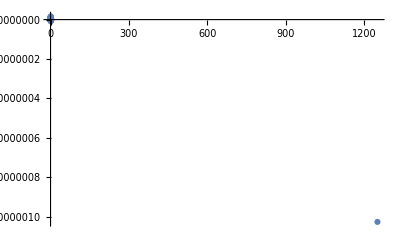

```mathematica
ListPlot[Data,PlotRange->Full]
```

```mathematica
PowerSpectralDensity[data,ω]
```

```mathematica
PowerSpectralDensity[data,ω]

PowerSpectralDensity[data,ω]
```

```mathematica
MaxFreq[samplecount_,seconds_]:=samplecount/seconds/2//N
```

```mathematica
ScientificForm[N[25000000,8]]
```

2.5000000×10^7

```mathematica
(*Some Important Quantities*)

(*Memory Depth of Oscilloscope = 5000, but sampling = 100MS/s*)

(*The Nyquist frequency is the highest frequency that any real-time digitizing oscilloscope can acquire without aliasing.*)

(*This frequency is half of the sample rate.*)

Nyquist[t_]:=5000/2/t//N
1s==Nyquist[1]
10s == Nyquist[10]
15s==Nyquist[15]
20s==Nyquist[20]
30s==Nyquist[30]
60s==Nyquist[60]
```

s==2500.

10 s==250.

15 s==166.667

20 s==125.

30 s==83.3333

60 s==41.6667

```mathematica
(*Paper suggests loss at ~130Hz and above*)

(*20 sec waveform may be good enough*)
```